WolframAlphaQueryNoResults

```mathematica
Npoints = 2000;
```

```mathematica
np=RandomReal[{-1,1},{Npoints,2}];
```

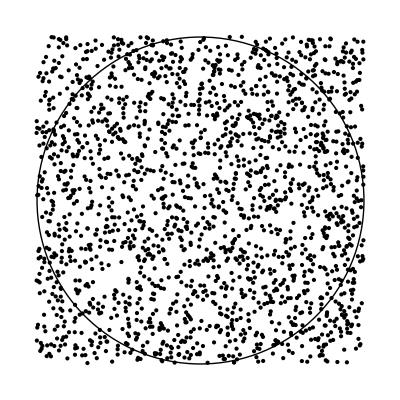

```mathematica
Print[Graphics[{Circle[{0,0},1],Point[np]}]]
```

```mathematica
mags=Map[Sqrt[#.#]&,np];
```

```mathematica
incircle=Select[mags, # <1 &];
outcircle=Select[mags, # >1 &];
```

```mathematica
piEst=4 Length[incircle]/Length[np] //N
```

3.152

```mathematica
(*below code is better but i didn't write it*)
```

```mathematica
approxPi[n_]:=4. Count[Map[Norm,RandomReal[{-1,1},{n,2}]],_?(#≤1&)]/n
```

```mathematica
approxPi[20000]
```

3.135